```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
```

```mathematica
Ndof=1+n+n(n+1)/2//.{n->m+1,m->3}//FullSimplify
```

15

```mathematica
pc[T_,μB_]:=Sum[Subscript[a, 2i,2j] T^(2i)μB^(2j)KroneckerDelta[2(i+j),4],{i,0,2},{j,0,2}];
pnonc[T_,μB_]:=T^4 Sum[Subscript[b, 2i,2j][T](μB/T)^(2i),{i,0,2}];
(*S[T_,μB_]:=1/2(1+Tanh[g(T^2+d μB^2-f)]);*)
p[T_,μB_]:=pc[T,μB]S[T,μB]+pnonc[T,μB](1-S[T,μB]);
s[T_,μB_]:=Evaluate[D[p[T,μB], T]];
ρB[T_,μB_]:=Evaluate[D[p[T,μB], μB]];
e[T_,μB_]:=T s[T,μB]+μB ρB[T,μB]-p[T,μB];
χTT[T_,μB_]:=Evaluate[D[p[T,μB], T,T]];
χTμB[T_,μB_]:=Evaluate[D[p[T,μB], T,μB]];
χμBμB[T_,μB_]:=Evaluate[D[p[T,μB], μB,μB]];
```

```mathematica
e[T,μB]//FullSimplify

p[T,μB]//FullSimplify
s[T,μB]//FullSimplify
ρB[T,μB]//FullSimplify
χTT[T,μB]//FullSimplify
χTμB[T,μB]//FullSimplify
χμBμB[T,μB]//FullSimplify
```

-b_(0,0)+μB^2 b_(2,0)+T^2 (b_(0,2)+3 T^2 b_(0,4)+3 μB^2 b_(2,2))+3 μB^4 b_(4,0)

b_(0,0)+μB^2 b_(2,0)+T^2 (b_(0,2)+T^2 b_(0,4)+μB^2 b_(2,2))+μB^4 b_(4,0)

2 T (b_(0,2)+2 T^2 b_(0,4)+μB^2 b_(2,2))

2 μB (b_(2,0)+T^2 b_(2,2)+2 μB^2 b_(4,0))

2 (b_(0,2)+6 T^2 b_(0,4)+μB^2 b_(2,2))

4 T μB b_(2,2)

2 (b_(2,0)+T^2 b_(2,2)+6 μB^2 b_(4,0))

```mathematica
T^4 Sum[Subscript[c, i](μB/T)^(2i),{i,0,2}]//FullSimplify
```

T^4 c_0+T^2 μB^2 c_1+μB^4 c_2

```mathematica
pnonc[T_,μB_]:=Sum[Subscript[b, 2i,2j] μB^(2i)T^(2j)If[2(i+j)>4,0,1],{i,0,2},{j,0,2}];
{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g}//MatrixForm//FullSimplify
Solve[{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g},{a,b,c,d,f,g}]//FullSimplify//Transpose//MatrixForm
```

(a+c T^2+d T^4+(b+f T^2) μB^2+g μB^4==p0
s0==2 T (c+2 d T^2+f μB^2)
2 μB (b+f T^2+2 g μB^2)==ρB0
2 (c+6 d T^2+f μB^2)==χTT0
4 f T μB==χTμB0
2 (b+f T^2+6 g μB^2)==χμBμB0)

(a→1/8 (8 p0-5 s0 T+T^2 χTT0+μB (-5 ρB0+2 T χTμB0+μB χμBμB0))
b→-(-3 ρB0+T χTμB0+μB χμBμB0)/(4 μB)
c→-(-3 s0+T χTT0+μB χTμB0)/(4 T)
d→-(s0-T χTT0)/(8 T^3)
f→χTμB0/(4 T μB)
g→-(ρB0-μB χμBμB0)/(8 μB^3))

```mathematica
Table[Coefficient[list,#]&/@{a,b,c,d,f,g},{list,{pnonc[T,μB],D[pnonc[T,μB],T],D[pnonc[T,μB],μB],D[pnonc[T,μB],{T,2}],D[pnonc[T,μB],T,μB],D[pnonc[T,μB],{μB,2}]}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g}//FullSimplify}]
%//Det
```

{{1,μB^2,T^2,T^4,T^2 μB^2,μB^4},{0,0,2 T,4 T^3,2 T μB^2,0},{0,2 μB,0,0,2 T^2 μB,4 μB^3},{0,0,2,12 T^2,2 μB^2,0},{0,0,0,0,4 T μB,0},{0,2,0,0,2 T^2,12 μB^2}}

-1024 T^4 μB^4

```mathematica
pnonc[T_,μB_]:=Sum[Subscript[b, 2i,2j] μB^(2i)T^(2j)If[2(i+j)>4,0,1],{i,0,2},{j,0,2}];
{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g}//MatrixForm//FullSimplify
Solve[{pnonc[T,μB]==p0,D[pnonc[T,μB],T]==s0,D[pnonc[T,μB],μB]==ρB0,D[pnonc[T,μB],{T,2}]==χTT0,D[pnonc[T,μB],T,μB]==χTμB0,D[pnonc[T,μB],{μB,2}]==χμBμB0}//.{Subscript[b, 0,0]->a,Subscript[b, 2,0]->b,Subscript[b, 0,2]->c,Subscript[b, 0,4]->d,Subscript[b, 2,2]->f,Subscript[b, 4,0]->g},{a,b,c,d,f,g}]//FullSimplify//Transpose//MatrixForm
```

```mathematica
pc[T_,μB_,μS_,μQ_]:=Sum[Subscript[a, 2i,2j,2k,2l] T^(2i)μB^(2j)μS^(2k)μQ^(2l)If[2(i+j+k+l)==4,1,0],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]
p[T_,μB_,μS_,μQ_]:=pc[T,μB,μS,μQ];
s[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T]];
ρB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB]];
ρS[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μS]];
ρQ[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μQ]];
e[T_,μB_,μS_,μQ_]:=T s[T,μB,μS,μQ]+μB ρB[T,μB,μS,μQ]+μS ρS[T,μB,μS,μQ]+μQ ρQ[T,μB,μS,μQ]-p[T,μB,μS,μQ];
e[T,μB,μS,μQ]==3p[T,μB,μS,μQ]//FullSimplify
```

True

```mathematica
(*entropy density*)
cfs=DeleteCases[Table[Subscript[b, 2i,2j,2k,2l] If[2(i+j+k+l)>4,0,1],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]//Flatten,0];
pnonc[T_,μB_,μS_,μQ_]:=Sum[Subscript[b, 2i,2j,2k,2l] T^(2i)μB^(2j)μS^(2k)μQ^(2l)If[2(i+j+k+l)>4,0,1],{i,0,2},{j,0,2},{k,0,2},{l,0,2}];
eqs={pnonc[T,μB,μS,μQ]==p0,
D[pnonc[T,μB,μS,μQ],T]==s0,
D[pnonc[T,μB,μS,μQ],μB]==ρB0,
D[pnonc[T,μB,μS,μQ],μS]==ρS0,
D[pnonc[T,μB,μS,μQ],μQ]==ρQ0,
D[pnonc[T,μB,μS,μQ],{T,2}]==χTT0,
D[pnonc[T,μB,μS,μQ],T,μB]==χTB0,
D[pnonc[T,μB,μS,μQ],T,μS]==χTS0,
D[pnonc[T,μB,μS,μQ],T,μQ]==χTQ0,
D[pnonc[T,μB,μS,μQ],{μB,2}]==χBB0,
D[pnonc[T,μB,μS,μQ],{μS,2}]==χSS0,
D[pnonc[T,μB,μS,μQ],{μQ,2}]==χQQ0,
D[pnonc[T,μB,μS,μQ],μB,μS]==χBS0,
D[pnonc[T,μB,μS,μQ],μB,μQ]==χBQ0,
D[pnonc[T,μB,μS,μQ],μS,μQ]==χSQ0
};
Length/@{eqs,cfs}
(sol=Solve[eqs,cfs]//FullSimplify//Transpose)//MatrixForm
```

{15,15}

(b_(0,0,0,0)→1/8 (8 p0-5 μS ρS0+μB^2 χBB0+μB (-5 ρB0+2 μQ χBQ0+2 μS χBS0)+μQ (-5 ρQ0+μQ χQQ0+2 μS χSQ0)+μS^2 χSS0+T (-5 s0+2 μB χTB0+2 μQ χTQ0+2 μS χTS0+T χTT0))
b_(0,0,0,2)→-(-3 ρQ0+μB χBQ0+μQ χQQ0+μS χSQ0+T χTQ0)/(4 μQ)
b_(0,0,0,4)→-(ρQ0-μQ χQQ0)/(8 μQ^3)
b_(0,0,2,0)→-(-3 ρS0+μB χBS0+μQ χSQ0+μS χSS0+T χTS0)/(4 μS)
b_(0,0,2,2)→χSQ0/(4 μQ μS)
b_(0,0,4,0)→-(ρS0-μS χSS0)/(8 μS^3)
b_(0,2,0,0)→-(-3 ρB0+μB χBB0+μQ χBQ0+μS χBS0+T χTB0)/(4 μB)
b_(0,2,0,2)→χBQ0/(4 μB μQ)
b_(0,2,2,0)→χBS0/(4 μB μS)
b_(0,4,0,0)→-(ρB0-μB χBB0)/(8 μB^3)
b_(2,0,0,0)→-(-3 s0+μB χTB0+μQ χTQ0+μS χTS0+T χTT0)/(4 T)
b_(2,0,0,2)→χTQ0/(4 T μQ)
b_(2,0,2,0)→χTS0/(4 T μS)
b_(2,2,0,0)→χTB0/(4 T μB)
b_(4,0,0,0)→-(s0-T χTT0)/(8 T^3))

```mathematica
pnonc[T,μB,μS,μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],T]//FullSimplify
D[pnonc[T,μB,μS,μQ],μB]//FullSimplify
D[pnonc[T,μB,μS,μQ],μS]//FullSimplify
D[pnonc[T,μB,μS,μQ],μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],{T,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],T,μB]//FullSimplify
D[pnonc[T,μB,μS,μQ],T,μS]//FullSimplify
D[pnonc[T,μB,μS,μQ],T,μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],{μB,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],{μS,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],{μQ,2}]//FullSimplify
D[pnonc[T,μB,μS,μQ],μB,μS]//FullSimplify
D[pnonc[T,μB,μS,μQ],μB,μQ]//FullSimplify
D[pnonc[T,μB,μS,μQ],μS,μQ]//FullSimplify
```

b_(0,0,0,0)+μQ^2 b_(0,0,0,2)+μQ^4 b_(0,0,0,4)+μS^2 b_(0,0,2,0)+μQ^2 μS^2 b_(0,0,2,2)+μS^4 b_(0,0,4,0)+μB^2 b_(0,2,0,0)+μB^2 μQ^2 b_(0,2,0,2)+μB^2 μS^2 b_(0,2,2,0)+μB^4 b_(0,4,0,0)+T^2 b_(2,0,0,0)+T^2 μQ^2 b_(2,0,0,2)+T^2 μS^2 b_(2,0,2,0)+T^2 μB^2 b_(2,2,0,0)+T^4 b_(4,0,0,0)

2 T (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+2 T^2 b_(4,0,0,0))

2 μB (b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+2 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0))

2 μS (b_(0,0,2,0)+μQ^2 b_(0,0,2,2)+2 μS^2 b_(0,0,4,0)+μB^2 b_(0,2,2,0)+T^2 b_(2,0,2,0))

2 μQ (b_(0,0,0,2)+2 μQ^2 b_(0,0,0,4)+μS^2 b_(0,0,2,2)+μB^2 b_(0,2,0,2)+T^2 b_(2,0,0,2))

2 (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+6 T^2 b_(4,0,0,0))

4 T μB b_(2,2,0,0)

4 T μS b_(2,0,2,0)

4 T μQ b_(2,0,0,2)

2 (b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+6 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0))

2 (b_(0,0,2,0)+μQ^2 b_(0,0,2,2)+6 μS^2 b_(0,0,4,0)+μB^2 b_(0,2,2,0)+T^2 b_(2,0,2,0))

2 (b_(0,0,0,2)+6 μQ^2 b_(0,0,0,4)+μS^2 b_(0,0,2,2)+μB^2 b_(0,2,0,2)+T^2 b_(2,0,0,2))

4 μB μS b_(0,2,2,0)

4 μB μQ b_(0,2,0,2)

4 μQ μS b_(0,0,2,2)

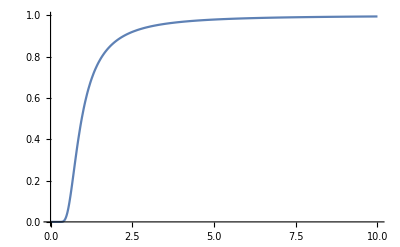

```mathematica
Plot[2/(Exp[1/x^2]+1),{x,0,10},PlotRange->All]
```

```mathematica
Θ[x_]:=2/(Exp[1/x^2]+1);
pc[T_,μB_,μS_,μQ_]:=Sum[Subscript[a, 2i,2j,2k,2l] T^(2i)μB^(2j)μS^(2j)μQ^(2j)KroneckerDelta[2(i+j+k+l),4],{i,0,2},{j,0,2},{k,0,2},{l,0,2}];
p[T_,μB_,μS_,μQ_]:=pc[T,μB,μS,μQ]S[T]+pnonc[T,μB,μS,μQ](1-S[T]);
s[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T]];
ρB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB]];
e[T_,μB_,μS_,μQ_]:=T s[T,μB,μS,μQ]+μB ρB[T,μB,μS,μQ]-p[T,μB,μS,μQ];
χTT[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T,T]];
χTμB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], T,μB]];
χμBμB[T_,μB_,μS_,μQ_]:=Evaluate[D[p[T,μB,μS,μQ], μB,μB]];
```

```mathematica
e[T,μB,μS,μQ]//FullSimplify
p[T,μB,μS,μQ]//FullSimplify
s[T,μB,μS,μQ]//FullSimplify
ρB[T,μB,μS,μQ]//FullSimplify
χTT[T,μB,μS,μQ]//FullSimplify
χTμB[T,μB,μS,μQ]//FullSimplify
χμBμB[T,μB,μS,μQ]//FullSimplify
```

-S[T] (a_(0,0,0,4)+a_(0,0,2,2)+a_(0,0,4,0)+T^2 (a_(2,0,0,2)+a_(2,0,2,0))+μB^2 μQ^2 μS^2 (a_(0,2,0,2)+a_(0,2,2,0)+μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))+T^4 a_(4,0,0,0))+μB (2 μB μQ^2 μS^2 S[T] (a_(0,2,0,2)+a_(0,2,2,0)+2 μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))-2 μB (-1+S[T]) (b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+2 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0)))+(-1+S[T]) (b_(0,0,0,0)+μQ^2 b_(0,0,0,2)+μQ^4 b_(0,0,0,4)+μS^2 b_(0,0,2,0)+μQ^2 μS^2 b_(0,0,2,2)+μS^4 b_(0,0,4,0)+μB^2 b_(0,2,0,0)+μB^2 μQ^2 b_(0,2,0,2)+μB^2 μS^2 b_(0,2,2,0)+μB^4 b_(0,4,0,0)+T^2 b_(2,0,0,0)+T^2 μQ^2 b_(2,0,0,2)+T^2 μS^2 b_(2,0,2,0)+T^2 μB^2 b_(2,2,0,0)+T^4 b_(4,0,0,0))+T (2 T S[T] (a_(2,0,0,2)+a_(2,0,2,0)+μB^2 μQ^2 μS^2 a_(2,2,0,0)+2 T^2 a_(4,0,0,0))-2 T (-1+S[T]) (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+2 T^2 b_(4,0,0,0))+(a_(0,0,0,4)+a_(0,0,2,2)+a_(0,0,4,0)+T^2 (a_(2,0,0,2)+a_(2,0,2,0))+μB^2 μQ^2 μS^2 (a_(0,2,0,2)+a_(0,2,2,0)+μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))+T^4 a_(4,0,0,0)) S'[T]-(b_(0,0,0,0)+μQ^2 b_(0,0,0,2)+μQ^4 b_(0,0,0,4)+μS^2 b_(0,0,2,0)+μQ^2 μS^2 b_(0,0,2,2)+μS^4 b_(0,0,4,0)+μB^2 b_(0,2,0,0)+μB^2 μQ^2 b_(0,2,0,2)+μB^2 μS^2 b_(0,2,2,0)+μB^4 b_(0,4,0,0)+T^2 b_(2,0,0,0)+T^2 μQ^2 b_(2,0,0,2)+T^2 μS^2 b_(2,0,2,0)+T^2 μB^2 b_(2,2,0,0)+T^4 b_(4,0,0,0)) S'[T])

S[T] (a_(0,0,0,4)+a_(0,0,2,2)+a_(0,0,4,0)+T^2 (a_(2,0,0,2)+a_(2,0,2,0))+μB^2 μQ^2 μS^2 (a_(0,2,0,2)+a_(0,2,2,0)+μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))+T^4 a_(4,0,0,0))-(-1+S[T]) (b_(0,0,0,0)+μQ^2 b_(0,0,0,2)+μQ^4 b_(0,0,0,4)+μS^2 b_(0,0,2,0)+μQ^2 μS^2 b_(0,0,2,2)+μS^4 b_(0,0,4,0)+μB^2 b_(0,2,0,0)+μB^2 μQ^2 b_(0,2,0,2)+μB^2 μS^2 b_(0,2,2,0)+μB^4 b_(0,4,0,0)+T^2 b_(2,0,0,0)+T^2 μQ^2 b_(2,0,0,2)+T^2 μS^2 b_(2,0,2,0)+T^2 μB^2 b_(2,2,0,0)+T^4 b_(4,0,0,0))

2 T S[T] (a_(2,0,0,2)+a_(2,0,2,0)+μB^2 μQ^2 μS^2 a_(2,2,0,0)+2 T^2 a_(4,0,0,0))-2 T (-1+S[T]) (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+2 T^2 b_(4,0,0,0))+(a_(0,0,0,4)+a_(0,0,2,2)+a_(0,0,4,0)+T^2 (a_(2,0,0,2)+a_(2,0,2,0))+μB^2 μQ^2 μS^2 (a_(0,2,0,2)+a_(0,2,2,0)+μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))+T^4 a_(4,0,0,0)) S'[T]-(b_(0,0,0,0)+μQ^2 b_(0,0,0,2)+μQ^4 b_(0,0,0,4)+μS^2 b_(0,0,2,0)+μQ^2 μS^2 b_(0,0,2,2)+μS^4 b_(0,0,4,0)+μB^2 b_(0,2,0,0)+μB^2 μQ^2 b_(0,2,0,2)+μB^2 μS^2 b_(0,2,2,0)+μB^4 b_(0,4,0,0)+T^2 b_(2,0,0,0)+T^2 μQ^2 b_(2,0,0,2)+T^2 μS^2 b_(2,0,2,0)+T^2 μB^2 b_(2,2,0,0)+T^4 b_(4,0,0,0)) S'[T]

2 μB μQ^2 μS^2 S[T] (a_(0,2,0,2)+a_(0,2,2,0)+2 μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))-2 μB (-1+S[T]) (b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+2 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0))

2 S[T] (a_(2,0,0,2)+a_(2,0,2,0)+μB^2 μQ^2 μS^2 a_(2,2,0,0)+6 T^2 a_(4,0,0,0))-2 (-1+S[T]) (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+6 T^2 b_(4,0,0,0))+4 T (a_(2,0,0,2)+a_(2,0,2,0)+μB^2 μQ^2 μS^2 a_(2,2,0,0)+2 T^2 a_(4,0,0,0)) S'[T]-4 T (b_(2,0,0,0)+μQ^2 b_(2,0,0,2)+μS^2 b_(2,0,2,0)+μB^2 b_(2,2,0,0)+2 T^2 b_(4,0,0,0)) S'[T]+(a_(0,0,0,4)+a_(0,0,2,2)+a_(0,0,4,0)+T^2 (a_(2,0,0,2)+a_(2,0,2,0))+μB^2 μQ^2 μS^2 (a_(0,2,0,2)+a_(0,2,2,0)+μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))+T^4 a_(4,0,0,0)) S''[T]-(b_(0,0,0,0)+μQ^2 b_(0,0,0,2)+μQ^4 b_(0,0,0,4)+μS^2 b_(0,0,2,0)+μQ^2 μS^2 b_(0,0,2,2)+μS^4 b_(0,0,4,0)+μB^2 b_(0,2,0,0)+μB^2 μQ^2 b_(0,2,0,2)+μB^2 μS^2 b_(0,2,2,0)+μB^4 b_(0,4,0,0)+T^2 b_(2,0,0,0)+T^2 μQ^2 b_(2,0,0,2)+T^2 μS^2 b_(2,0,2,0)+T^2 μB^2 b_(2,2,0,0)+T^4 b_(4,0,0,0)) S''[T]

2 μB (2 T μQ^2 μS^2 S[T] a_(2,2,0,0)-2 T (-1+S[T]) b_(2,2,0,0)+μQ^2 μS^2 (a_(0,2,0,2)+a_(0,2,2,0)+2 μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0)) S'[T]-(b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+2 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0)) S'[T])

2 μQ^2 μS^2 S[T] (a_(0,2,0,2)+a_(0,2,2,0)+6 μB^2 μQ^2 μS^2 a_(0,4,0,0)+T^2 a_(2,2,0,0))-2 (-1+S[T]) (b_(0,2,0,0)+μQ^2 b_(0,2,0,2)+μS^2 b_(0,2,2,0)+6 μB^2 b_(0,4,0,0)+T^2 b_(2,2,0,0))